## Introduction

Making movies for random pinning

## Sandbox

$Aborted

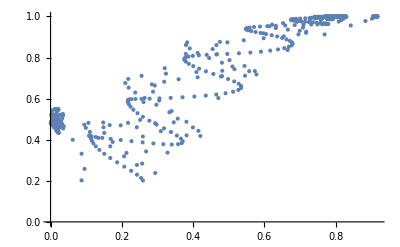

```mathematica
(*Preamble*)
{dt,n,T}={0.1,300,500}; 
{J,k}={0.5,0.5};
{e,b}={2.3,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomChoice[{RandomReal[{0π,2π}],RandomReal[{1.99π,2π}]}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]

ListPlot[{Wp//Abs,Wm//Abs}ᵀ,PlotRange->All,AxesOrigin->{0,0}]
```

## All states: old

### Make slides

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

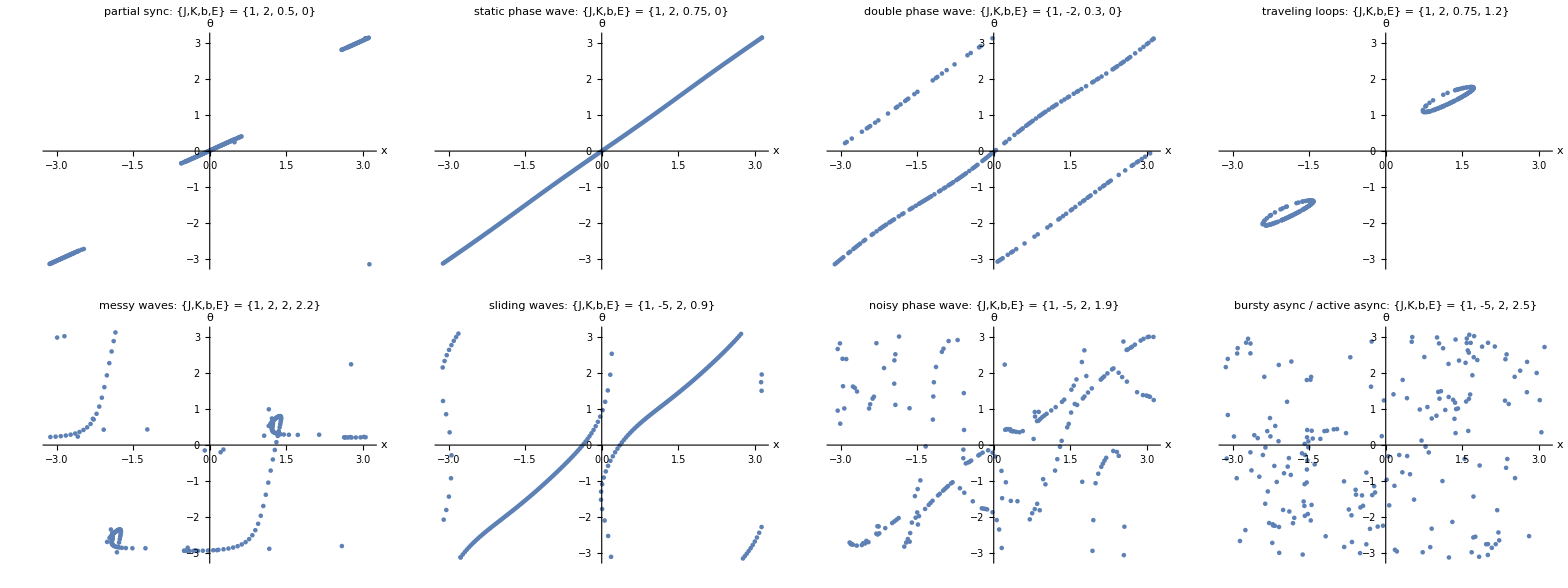

```mathematica
pars={
{1,2,0.5,0,"partial sync"},
{1,2,0.75,0,"static phase wave"},
{1,-2,0.3,0,"double phase wave"},
{1,2,0.75,1.2,"traveling loops"},
{1,2,2,2.2,"messy waves"},
{1,-5,2,0.9,"sliding waves"},
{1,-5,2,1.9,"noisy phase wave"},
{1,-5,2,2.5,"bursty async / active async"}
};

allSlides=ParallelTable[
(*Make slides*)
SeedRandom[0];
(*Preamble*)
{dt,n,T}={0.25,200,300}; 
{J,k,b,e,state}={par[[1]],par[[2]],par[[3]],par[[4]],par[[5]]};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
fig=plotResultsSingle[znew,state<>": {J,K,b,E} = "<>ToString[{J,k,b,e}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
Grid[{allSlides[[1;;4,-1]],allSlides[[5;;-1,-1]]}]
```

### Make movie

```mathematica
movieSlides=Table[Grid[{allSlides[[1;;4,t]],allSlides[[5;;-1,t]]}],{t,1,Dimensions[allSlides][[2]]}];
SetDirectory[NotebookDirectory[]];
Export["movies/all-states.mov",movieSlides]
```

movies/all-states.mov

## All states: new

### Make slides

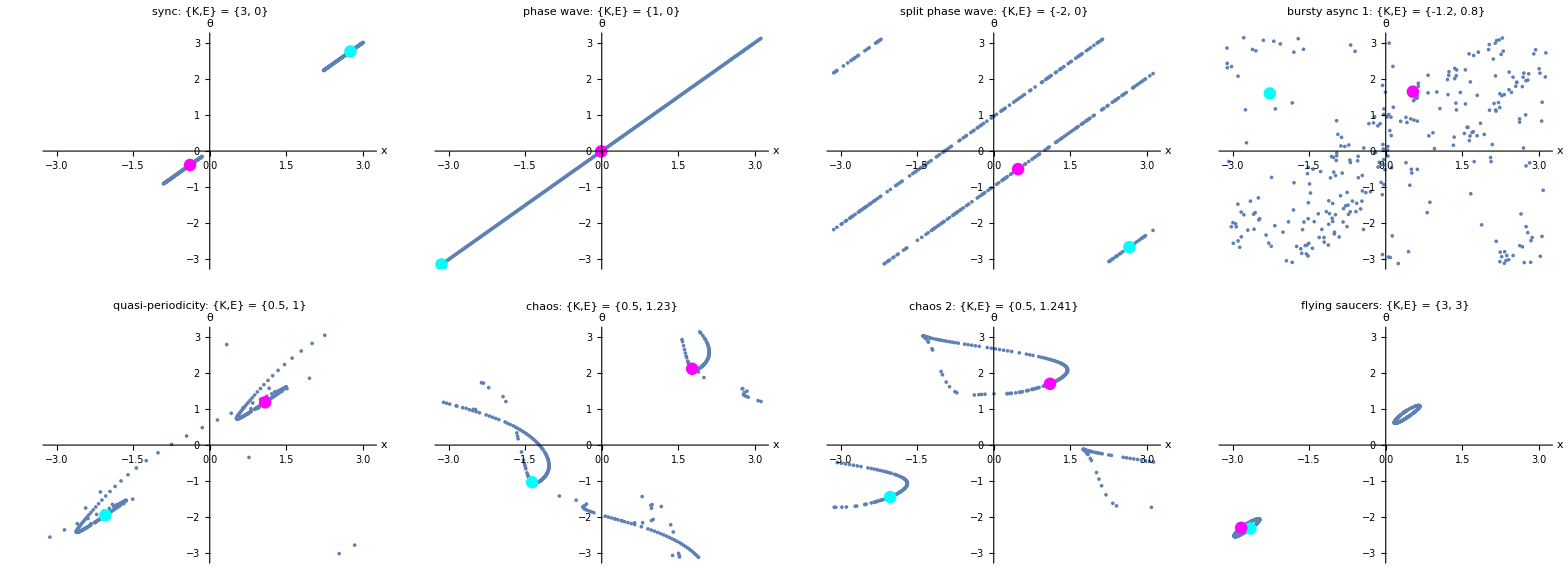

```mathematica
pars={
{3,3,1,0,"sync"},
{1,1,1,0,"phase wave"},
{-2,-2,1,0,"split phase wave"},
{-1.2,-1.2,1,0.8,"bursty async 1"},
{0.5,0.5,1,1,"quasi-periodicity"},
{0.5,0.5,1,1.23,"chaos"},
{0.5,0.5,1,1.241,"chaos 2"},
{3,3,1,3,"flying saucers"}
};

allSlides=ParallelTable[
(*Make slides*)
SeedRandom[0];
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k,b,e,state}={par[[1]],par[[2]],par[[3]],par[[4]],par[[5]]};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
fig=plotResultsSingle[znew,state<>": {K,E} = "<>ToString[{k,e}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
Grid[{allSlides[[1;;4,-1]],allSlides[[5;;-1,-1]]}]
```

### Make movie

```mathematica
movieSlides=Table[Grid[{allSlides[[1;;4,t]],allSlides[[5;;-1,t]]}],{t,1,Dimensions[allSlides][[2]]}];
SetDirectory[NotebookDirectory[]];
Export["movies/all-states-new.mov",movieSlides]
```

movies/all-states-new.mov

## Chaos

### Make slides

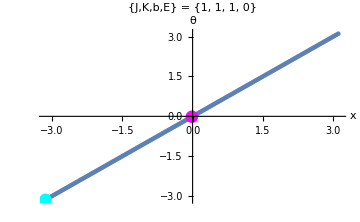
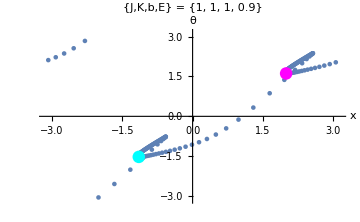
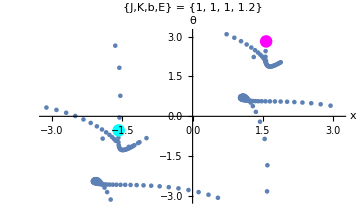
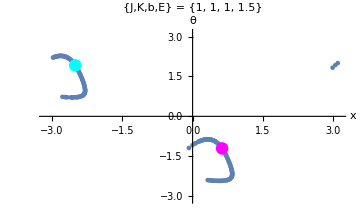
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |

```mathematica
pars={
{1,1,1,0,""},
{1,1,1,0.9,""},
{1,1,1,1.2,""},
{1,1,1,1.5,""}
};

allSlides=ParallelTable[
(*Make slides*)
SeedRandom[0];
(*Preamble*)
{dt,n,T}={0.25,200,100}; 
{J,k,b,e,state}={par[[1]],par[[2]],par[[3]],par[[4]],par[[5]]};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
fig=plotResultsSingle[znew,state<>" {K,E} = "<>ToString[{k,e}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
Grid[{allSlides[[1;;4,-1]],allSlides[[5;;-1,-1]]}]
```

### Make movie

```mathematica
movieSlides=Table[Grid[{allSlides[[1;;4,t]],allSlides[[5;;-1,t]]}],{t,1,Dimensions[allSlides][[2]]}];
SetDirectory[NotebookDirectory[]];
Export["movies/chaos.mov",movieSlides]
```

movies/chaos.mov

## Bistability

### New

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

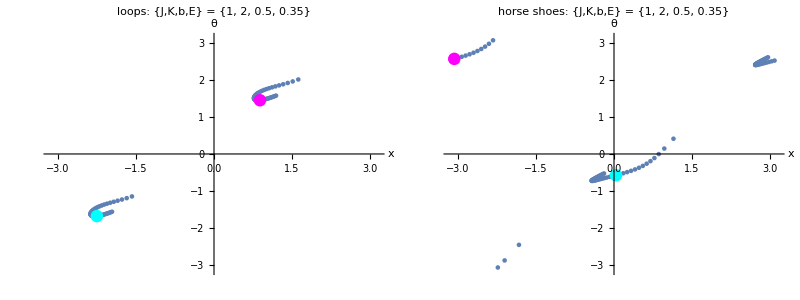

```mathematica
pars={
{1,2,0.5,0.35,0,"loops"},
{1,2,0.5,0.35,1.99,"horse shoes"}
};

allSlides=ParallelTable[
(*Make slides*)
SeedRandom[0];
(*Preamble*)
{dt,n,T}={0.25,100,200}; 
{J,k,b,e,ic,state}={par[[1]],par[[2]],par[[3]],par[[4]],par[[5]],par[[6]]};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomChoice[{RandomReal[{0π,2π}],RandomReal[{ic π,2π}]}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
fig=plotResultsSingle[znew,state<>": {J,K,b,E} = "<>ToString[{J,k,b,e}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
Grid[{allSlides[[1;;2,-1]]}]
```

```mathematica
movieSlides=Table[Grid[{allSlides[[1;;2,t]]}],{t,1,Dimensions[allSlides][[2]]}];
SetDirectory[NotebookDirectory[]];
Export["movies/traveling-loops-bistability-2.mov",movieSlides]
```

movies/traveling-loops-bistability-2.mov

### Old

```mathematica
pars={
{1,2,0.5,0.35,0,"loops"},
{1,2,0.5,0.35,1.99,"horse shoes"}
};

allSlides=ParallelTable[
(*Make slides*)
SeedRandom[0];
(*Preamble*)
{dt,n,T}={0.25,100,200}; 
{J,k,b,e,ic,state}={par[[1]],par[[2]],par[[3]],par[[4]],par[[5]],par[[6]]};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{ic*π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
fig=plotResultsSingle[znew,state<>": {J,K,b,E} = "<>ToString[{J,k,b,e}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
Grid[{allSlides[[1;;2,-1]]}]
```

```mathematica
movieSlides=Table[Grid[{allSlides[[1;;2,t]]}],{t,1,Dimensions[allSlides][[2]]}];
SetDirectory[NotebookDirectory[]];
Export["movies/traveling-loops-bistability-2.mov",movieSlides]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,x2,θ1,θ2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
{x,θ}={z[[1,All]],z[[2,All]]};
n=Dimensions[z][[2]];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResultsSingle[z_,label_]:=Block[{colors,Wp,Wm,p1,p2,p3,index,b,x,θ,x1,x2,θ1,θ2,n},
n=Dimensions[z][[2]];
{x,θ}={z[[1,All]],z[[2,All]]};
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,
PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},PlotLabel->Style[label,15,Black],
Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}
];
Return[p2]
];
```